Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data={};
radius=0.3;
nData=10000;
Do[
x=0.5+radius*i/nData*Cos[8*Pi*(i-1)/(nData-1)];
y=0.5+radius*i/nData*Sin[8*Pi*(i-1)/(nData-1)];
z=Sin[0.5*Pi*(i-1)/(nData-1)]//N;
AppendTo[data,{x,y,z}];
,{i,1,nData}];
```

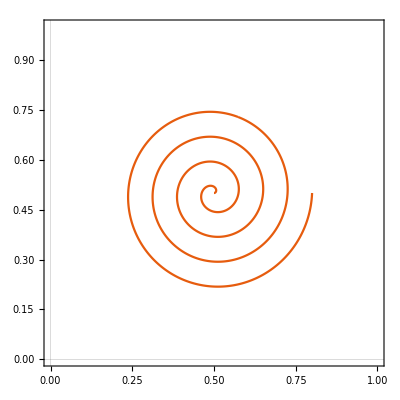

```mathematica
plt1=ListLinePlot[data[[;;,{1,2}]],AspectRatio->1,PlotRange->{{0,1},{0,1}}]
```

```mathematica
plt2=Show[
ListPointPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}}],
ListPointPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}}]/.Point->Line
]
```

-Graphics3D-

```mathematica
pltR=Grid[{{plt1,plt2}}]
```

-Graphics- | -Graphics3D-

```mathematica
Export["figures/path.png",pltR,ImageResolution->150]
```

figures/path.png

```mathematica
f=OpenWrite["path.txt"];
Do[
s=ToString[pt[[1]]]<>" "<>ToString[pt[[2]]]<>" "<>ToString[pt[[3]]];
WriteLine[f,s];
,{pt,data}];
Close[f];
```